```mathematica
inverseb[x_]:=(Normal[InverseSeries[Series[BesselJ[1,y],{y,0,20}]]])/.y->x//N
sim[dd_, scale_, exp_]:= Module[{d, sc, expp},  d=dd; sc =scale; expp=exp; 
ϕ = d[[1]];
amplitude[t_]:=Module[{tt},  tt=t;
ret=0;
For[m=0, m≤ Length[d]-2, m++,
If[m==0, scalar=a/2,scalar=a];
ret+=inverseb[scalar*d[[m+2]]]*Cos[m*ϕ + m*ω*tt]];
ret];
ω = 2*π*180;
U = 2π*1;
a = .1;
end = (π/(a*U*2))*sc; (* twice for no precomp*)
up=1/Sqrt[2];
down=1/Sqrt[2];
h=0; 
For[i=0, i≤Length[d]-2, i++,
h += U*Cos[i*ω*x-π/2 + amplitude[x]]];
s=NDSolve[{ⅈ*y'[x]==h*y[x] ,y[0]==up},y,{x,0,end}, MaxSteps->Infinity];
up = Evaluate[y[end]/.s][[1]];
s=NDSolve[{ⅈ*y'[x]==-h*y[x] ,y[0]==down},y,{x,0,end}, MaxSteps->Infinity];
down = Evaluate[y[end]/.s][[1]];
If[expp==1,Re[up*Conjugate[down] + down*Conjugate[up]],{{Re[up], Im[up]}, {Re[down], Im[down]}}]];
```

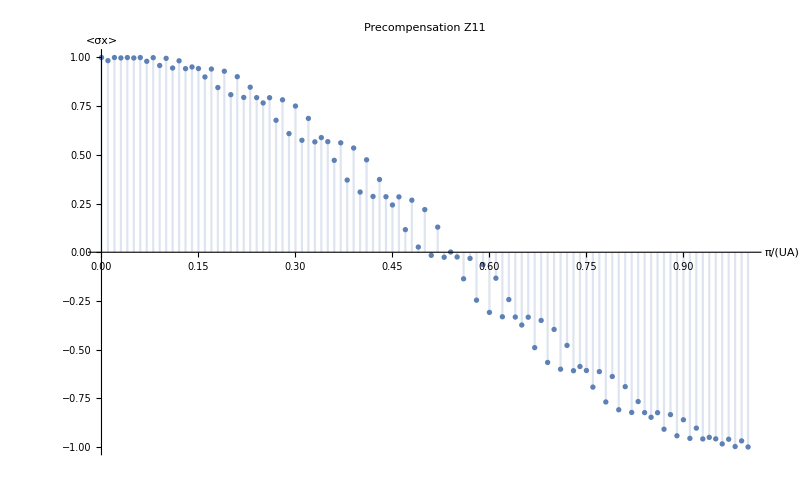

```mathematica
s=Import["~/repos/single_site_addressability/final_notebooks/z11.csv","String"];
data11=ImportString[StringReplace[s," "->""],"Data"];
DiscretePlot[sim[data11[[32]], sc, 1], {sc, 0 ,1, .01}, PlotLabel->"Precompensation Z11", AxesLabel->{"π/(UA)", "<σx>"}]
```

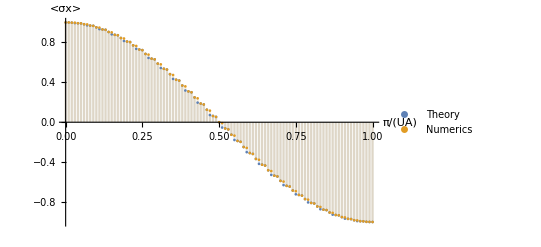

```mathematica
(*Theory*)
ω = 2*π*180;
U = 2π*1;
a = .1;
t = (π/(a*U*2))*sc;
Θ = a*2*U*t;
ϕ=π;
correction = Sum[(4*U*BesselJ[n, inverseb[a]]*Sin[1/2*(n+1)*t*ω]*Cos[n*ϕ + 1/2*(π-2*t*ω)-π/2])/((n+1)*ω), {n,0, 100}];
correction +=Sum[(4*U*BesselJ[n, inverseb[a]]*Sin[1/2*(n+1)*t*ω]*Cos[n*ϕ + 1/2*(π-2*t*ω)-π/2])/((n+1)*ω), {n,-100, -2}];
DiscretePlot[{Cos[Θ]-Sin[Θ]*correction,sim[data11[[32]], sc, 1]}, {sc, 0, 1, .01},  AxesLabel->{Style["π/(UA)", FontSize->24], Style["<σx>", FontSize->24]}, PlotLegends->{Style["Theory", 24], Style["Numerics", 24]}, BaseStyle->{FontSize->24}]
```

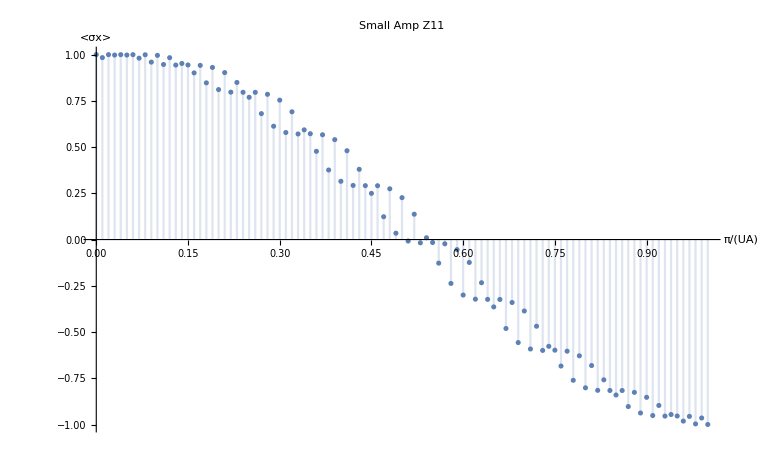

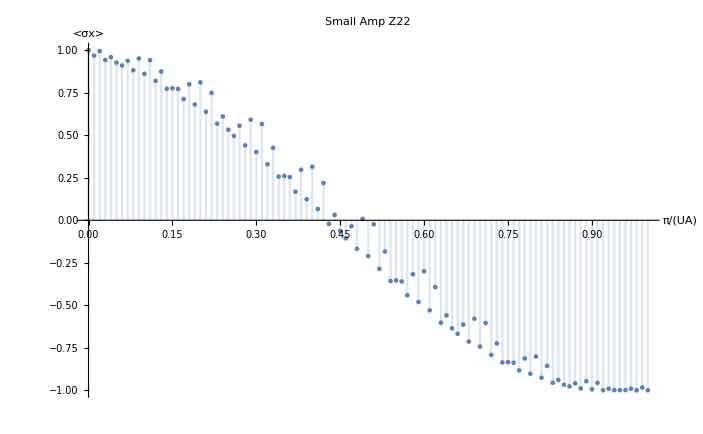

```mathematica
sim[dd_, scale_, exp_]:= Module[{d, sc, expp},  d=dd; sc =scale; expp=exp; 
ϕ = d[[1]];
amplitude[t_]:=Module[{tt},  tt=t;
ret=0;
For[m=0, m≤ Length[d]-2, m++,
If[m==0, scalar=a/2,scalar=a];
ret+=scalar*d[[m+2]]*Cos[m*ϕ + m*ω*tt]];
ret];
ω = 2*π*18;
U = 2π*1;
a = .2;
end = (π/(a*U))*sc; (* twice for no precomp*)
up=1/Sqrt[2];
down=1/Sqrt[2];
h=0; 
For[i=0, i≤Length[d]-2, i++,
h += U*Cos[i*ω*x-π/2 + amplitude[x]]];
s=NDSolve[{ⅈ*y'[x]==h*y[x] ,y[0]==up},y,{x,0,end}, MaxSteps->Infinity];
up = Evaluate[y[end]/.s][[1]];
s=NDSolve[{ⅈ*y'[x]==-h*y[x] ,y[0]==down},y,{x,0,end}, MaxSteps->Infinity];
down = Evaluate[y[end]/.s][[1]];
If[expp==1,Re[up*Conjugate[down] + down*Conjugate[up]],{{Re[up], Im[up]}, {Re[down], Im[down]}}]];
(* For Z11 *)
s=Import["~/repos/single_site_addressability/final_notebooks/z11.csv","String"];
data11=ImportString[StringReplace[s," "->""],"Data"];
DiscretePlot[sim[data11[[32]], sc, 1], {sc, 0 ,1, .01}, PlotLabel->"Small Amp Z11",AxesLabel->{"π/(UA)", "<σx>"},AxesLabel->{Style["π/(UA)", FontSize->24], Style["<σx>", FontSize->24]}, BaseStyle->{FontSize->24}]
(* For Z22 *)
s=Import["~/repos/single_site_addressability/final_notebooks/z22.csv","String"];
data22=ImportString[StringReplace[s," "->""],"Data"];
DiscretePlot[sim[data22[[32]], sc, 1], {sc, 0 ,1, .01}, PlotLabel->"Small Amp Z22",AxesLabel->{"π/(UA)", "<σx>"}, AxesLabel->{Style["π/(UA)", FontSize->24], Style["<σx>", FontSize->24]}, BaseStyle->{FontSize->24}]
```

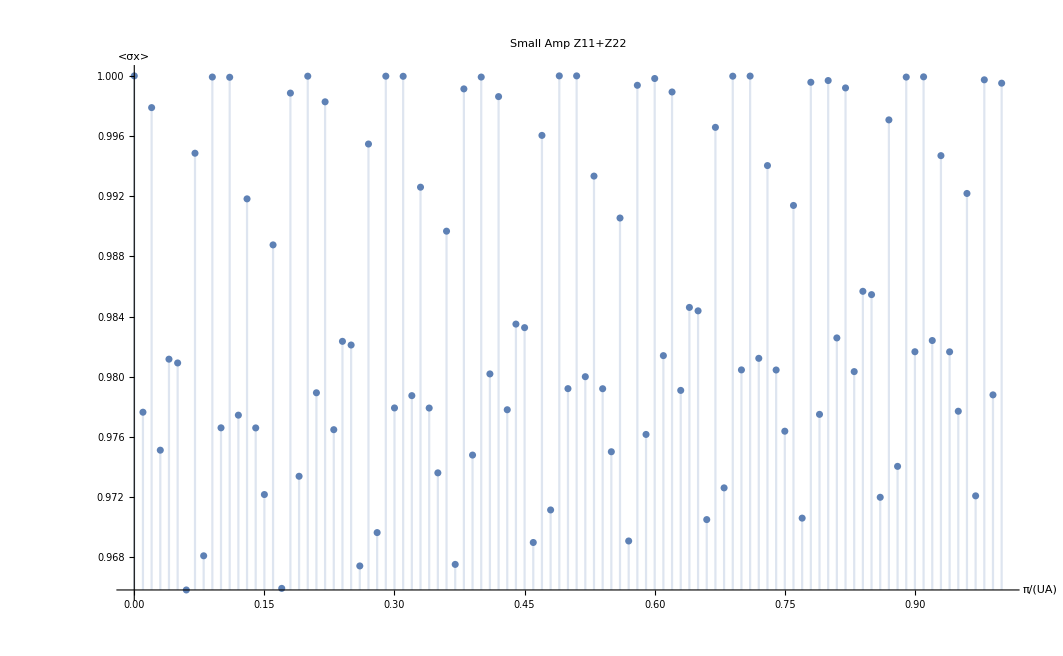

```mathematica
(* For Z11+Z22 *)
s=Import["~/repos/single_site_addressability/final_notebooks/z1122.csv","String"];
data1122=ImportString[StringReplace[s," "->""],"Data"];
DiscretePlot[sim[data1122[[32]], sc, 1], {sc, 0 ,1, .01}, PlotLabel->"Small Amp Z11+Z22",AxesLabel->{"π/(UA)", "<σx>"}, AxesLabel->{Style["π/(UA)", FontSize->24], Style["<σx>", FontSize->24]}, BaseStyle->{FontSize->24}]
```

```mathematica
s=Import["~/repos/single_site_addressability/final_notebooks/elliptical2040.csv","String"];
data=ImportString[StringReplace[s," "->""],"Data"];
DiscretePlot[sim[data[[1]], k, 1],{k, 0, 1, .1}]
```

$Aborted

```mathematica
s=Import["/home/ampolloreno/repos/single_site_addressability/final_notebooks/elliptical3212.csv","String"];
data=ImportString[StringReplace[s," "->""],"Data"];
simfull[dd_]:=sim[dd, 1, 0]
Map[simfull, data]
```

{{{0.000430385,-0.707108},{0.000430385,0.707108}},{{0.234405,-0.667124},{0.234405,0.667124}},{{0.590606,-0.388828},{0.590606,0.388828}},{{0.697398,-0.116789},{0.697398,0.116789}},{{0.706754,-0.0223893},{0.706754,0.0223893}},{{0.70705,-0.0089852},{0.70705,0.0089852}},{{0.707009,-0.0115778},{0.707009,0.0115778}},{{0.707086,-0.00548415},{0.707086,0.00548415}},{{0.706726,-0.02325},{0.706726,0.02325}},{{0.696956,-0.119399},{0.696956,0.119399}},{{0.592436,-0.386032},{0.592436,0.386032}},{{0.25926,-0.657866},{0.25926,0.657866}},{{0.0327805,-0.706349},{0.0327805,0.706349}},{{0.234406,-0.667123},{0.234406,0.667123}},{{0.592436,-0.386033},{0.592436,0.386033}},{{0.259258,-0.657866},{0.259258,0.657866}},{{0.0327815,-0.706349},{0.0327815,0.706349}},{{0.270842,-0.653182},{0.270842,0.653182}},{{0.603584,-0.368358},{0.603584,0.368358}},{{0.70063,-0.0954969},{0.70063,0.0954969}},{{0.351417,-0.613602},{0.351417,0.613602}},{{0.129416,-0.695164},{0.129416,0.695164}},{{0.376929,-0.59827},{0.376929,0.59827}},{{0.622809,-0.334827},{0.622809,0.334827}},{{0.703286,-0.0734087},{0.703286,0.0734087}},{{0.706972,-0.013871},{0.706972,0.013871}},{{0.707096,-0.00407948},{0.707096,0.00407948}},{{0.707103,-0.00278816},{0.707103,0.00278816}},{{0.707052,0.00891762},{0.707052,-0.00891762}},{{0.707087,-0.00551887},{0.707087,0.00551887}},{{0.707021,0.0110941},{0.707021,-0.0110941}},{{0.706903,-0.0170308},{0.706903,0.0170308}},{{0.707018,0.0112223},{0.707018,-0.0112223}},{{0.707055,-0.00866388},{0.707055,0.00866388}},{{0.707079,0.00650725},{0.707079,-0.00650725}},{{0.707106,-0.00195596},{0.707106,0.00195596}},{{0.707094,0.00434507},{0.707094,-0.00434507}},{{0.706963,-0.0143634},{0.706963,0.0143634}},{{0.699905,-0.100676},{0.699905,0.100676}},{{0.606429,-0.363657},{0.606429,0.363657}},{{0.310983,-0.635053},{0.310983,0.635053}},{{0.698207,-0.111847},{0.698207,0.111847}},{{0.706814,-0.0203898},{0.706814,0.0203898}},{{0.707107,0.0000524946},{0.707107,-0.0000524946}},{{0.707106,-0.00190083},{0.707106,0.00190083}},{{0.707093,0.00464686},{0.707093,-0.00464686}},{{0.707043,-0.00958336},{0.707043,0.00958336}},{{0.707076,0.00660638},{0.707076,-0.00660638}},{{0.707086,-0.0055522},{0.707086,0.0055522}},{{0.707097,-0.00401628},{0.707097,0.00401628}},{{0.706726,-0.0232489},{0.706726,0.0232489}},{{0.696955,-0.119397},{0.696955,0.119397}},{{0.590605,-0.388829},{0.590605,0.388829}},{{0.697397,-0.116793},{0.697397,0.116793}},{{0.706754,-0.0223966},{0.706754,0.0223966}},{{0.707086,-0.00548391},{0.707086,0.00548391}},{{0.707009,-0.0115774},{0.707009,0.0115774}},{{0.707051,-0.00898986},{0.707051,0.00898986}},{{0.700629,-0.0955001},{0.700629,0.0955001}},{{0.603585,-0.368358},{0.603585,0.368358}},{{0.270842,-0.653183},{0.270842,0.653183}},{{0.129415,-0.695164},{0.129415,0.695164}},{{0.310984,-0.635053},{0.310984,0.635053}},{{0.606429,-0.363657},{0.606429,0.363657}},{{0.698209,-0.111835},{0.698209,0.111835}},{{0.706814,-0.0203932},{0.706814,0.0203932}},{{0.707098,-0.00401688},{0.707098,0.00401688}},{{0.707086,-0.00555175},{0.707086,0.00555175}},{{0.707076,0.00661534},{0.707076,-0.00661534}},{{0.707042,-0.00958463},{0.707042,0.00958463}},{{0.707093,0.00464668},{0.707093,-0.00464668}},{{0.707105,-0.00190104},{0.707105,0.00190104}},{{0.707108,0.0000499976},{0.707108,-0.0000499976}},{{0.706963,-0.0143622},{0.706963,0.0143622}},{{0.699905,-0.100676},{0.699905,0.100676}},{{0.622809,-0.334827},{0.622809,0.334827}},{{0.376929,-0.598271},{0.376929,0.598271}},{{0.703286,-0.0734081},{0.703286,0.0734081}},{{0.706972,-0.0138718},{0.706972,0.0138718}},{{0.707094,0.00434542},{0.707094,-0.00434542}},{{0.707105,-0.00195632},{0.707105,0.00195632}},{{0.707079,0.0065106},{0.707079,-0.0065106}},{{0.707055,-0.00866537},{0.707055,0.00866537}},{{0.707018,0.0112242},{0.707018,-0.0112242}},{{0.706903,-0.0170212},{0.706903,0.0170212}},{{0.707021,0.0110922},{0.707021,-0.0110922}},{{0.707087,-0.0055179},{0.707087,0.0055179}},{{0.707052,0.00891817},{0.707052,-0.00891817}},{{0.707103,-0.00278511},{0.707103,0.00278511}},{{0.707096,-0.00407948},{0.707096,0.00407948}},{{0.351418,-0.613602},{0.351418,0.613602}}}

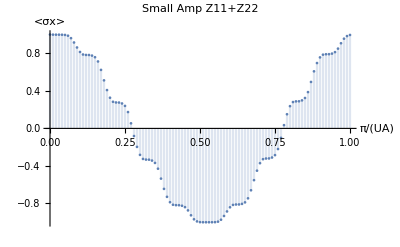

```mathematica
sim[dd_, scale_, exp_]:= Module[{d, sc, expp},  d=dd; sc =scale; expp=exp; 
ϕ = d[[1]];
amplitude[t_]:=Module[{tt},  tt=t;
ret=0;
For[m=0, m≤ Length[d]-2, m++,
If[m==0, scalar=a/2,scalar=a];
ret+=scalar*d[[m+2]]*Cos[m*ϕ + m*ω*tt]];
ret];
ω = 2*π*18;
U = 2π*1;
a = .2;
end = 2*(π/(a*U))*sc; (* twice for no precomp*)
up=1/Sqrt[2];
down=1/Sqrt[2];
h[x_]:=If[sc ≤.5 , U*Cos[ω*x-π/2 + amplitude[x]],  U*Cos[2*ω*x-π/2 + amplitude[x]]];
s=NDSolve[{ⅈ*y'[x]==h*y[x] ,y[0]==up},y,{x,0,end}, MaxSteps->Infinity];
up = Evaluate[y[end]/.s][[1]];
s=NDSolve[{ⅈ*y'[x]==-h*y[x] ,y[0]==down},y,{x,0,end}, MaxSteps->Infinity];
down = Evaluate[y[end]/.s][[1]];
If[expp==1,Re[up*Conjugate[down] + down*Conjugate[up]],{{Re[up], Im[up]}, {Re[down], Im[down]}}]];
(* For Z11+Z22 *)
s=Import["~/repos/single_site_addressability/final_notebooks/z1122.csv","String"];
data1122=ImportString[StringReplace[s," "->""],"Data"];
DiscretePlot[sim[data1122[[32]], sc, 1], {sc, 0 ,1, .01}, PlotLabel->"Small Amp Z11+Z22",AxesLabel->{"π/(UA)", "<σx>"}, AxesLabel->{Style["π/(UA)", FontSize->24], Style["<σx>", FontSize->24]}, BaseStyle->{FontSize->24}]
```

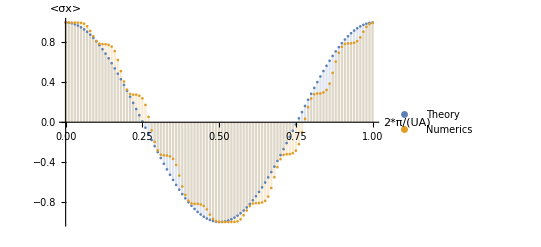

```mathematica
Analytics[sc_]:=Module[{scc}, scc=sc;
t = 4*(π/(a*U*2))*scc;
If [scc≤.5,Θ = 2*U*t*BesselJ[1, a],Θ = 2*U*t*BesselJ[1, a]]; 
ϕ=π;
(*correction = Sum[(4*U*BesselJ[n, inverseb[a]]*Sin[1/2*(n+1)*t*ω]*Cos[n*ϕ + 1/2*(π-2*t*ω)-π/2])/((n+1)*ω), {n,0, 100}];
correction +=Sum[(4*U*BesselJ[n, inverseb[a]]*Sin[1/2*(n+1)*t*ω]*Cos[n*ϕ + 1/2*(π-2*t*ω)-π/2])/((n+1)*ω), {n,-100, -2}];*)
correction=0;
Cos[Θ]-Sin[Θ]*correction
]

DiscretePlot[{Analytics[sc],sim[data11[[32]], sc, 1]}, {sc, 0, 1, .01},  AxesLabel->{Style["2*π/(UA)", FontSize->24], Style["<σx>", FontSize->24]}, PlotLegends->{Style["Theory", 24], Style["Numerics", 24]}, BaseStyle->{FontSize->24}]
```

0.1

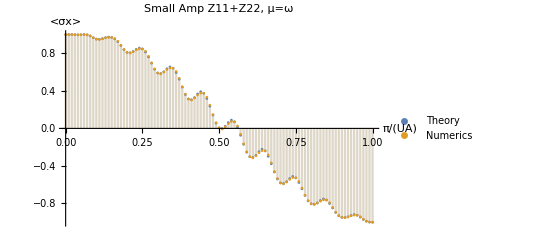

```mathematica
sim[dd_, scale_, exp_]:= Module[{d, sc, expp},  d=dd; sc =scale; expp=exp; 
ϕ = d[[1]];
amplitude[t_]:=Module[{tt},  tt=t;
ret=0;
For[m=0, m≤ Length[d]-2, m++,
If[m==0, scalar=a/2,scalar=a];
ret+=scalar*d[[m+2]]*Cos[m*ϕ + m*ω*tt]];
ret];
ω = 2*π*18;
U = 2π*1;
a = .1;
end = (π/(a*U))*sc; (* twice for no precomp*)
up=1/Sqrt[2];
down=1/Sqrt[2];
h = U*Cos[ω*x-π/2 + amplitude[x]];
s=NDSolve[{ⅈ*y'[x]==h*y[x] ,y[0]==up},y,{x,0,end}, MaxSteps->Infinity];
up = Evaluate[y[end]/.s][[1]];
s=NDSolve[{ⅈ*y'[x]==-h*y[x] ,y[0]==down},y,{x,0,end}, MaxSteps->Infinity];
down = Evaluate[y[end]/.s][[1]];
If[expp==1,Re[up*Conjugate[down] + down*Conjugate[up]],{{Re[up], Im[up]}, {Re[down], Im[down]}}]];




A=.1
ω = 2*π*18;
U = 2π*1;
T= (π/(A*U))*sc;
Θ =U/2* Sum[((-ⅈ)^b+ⅈ^b) T BesselJ[-1-2 b,A] BesselJ[b,A], {b, -10, 10}];
extras = U/2*Sum[Integrate[ Exp[I*(-ω*t-π/2)] * I^(a+b)*BesselJ[a, A]*BesselJ[b,A]*Exp[I*(a*(π-ω*t)+b*(2*π-2*ω*t))] + Exp[-I*(-ω*t-π/2)] * (-I)^(a+b)*BesselJ[a, A]*BesselJ[b,A]*Exp[-I*(a*(π-ω*t)+b*(2*π-2*ω*t))], {t, 0, F}] Boole[-1 !=( a + 2b)], {a, -20, 20}, {b, -20, 20}]/.F->T;

toplot = Cos[2*(Θ-extras)];
(* For Z11+Z22 *)
s=Import["~/repos/single_site_addressability/final_notebooks/z1122.csv","String"];
data1122=ImportString[StringReplace[s," "->""],"Data"];
DiscretePlot[{toplot, sim[data1122[[32]], sc, 1]}, {sc, 0 ,1, .01}, PlotLabel->"Small Amp Z11+Z22, μ=ω",AxesLabel->{"π/(UA)", "<σx>"}, AxesLabel->{Style["π/(UA)", FontSize->24], Style["<σx>", FontSize->24]}, BaseStyle->{FontSize->24},PlotLegends->{Style["Theory", 24], Style["Numerics", 24]}, BaseStyle->{FontSize->24}]
```

```mathematica
Analytics[1]
```

ReplaceAll::reps: {NDSolve[{ⅈ y'[x]=={0.,0.,0.,0.},y[0]==1/(√2)},y,{x,0,1/2},MaxSteps→∞]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

2 Re[Conjugate[y[1/2]] y[1/2]]

```mathematica
Analytics[sc_]:=Module[{scc}, scc=sc;
up=1/Sqrt[2];
down=1/Sqrt[2];
U = 2π*1;
ω = 2*π*18;
a = .05;
end = (π/(a*U))*sc;
h= U*BesselJ[-1,a*data1122[[32]][[3]]]*BesselJ[0,a*data1122[[32]][[4]]] ;
s=NDSolve[{ⅈ*y'[x]==h*y[x] ,y[0]==up},y,{x,0,end}, MaxSteps->Infinity];
up = Evaluate[y[end]/.s][[1]];
s=NDSolve[{ⅈ*y'[x]==-h*y[x] ,y[0]==down},y,{x,0,end}, MaxSteps->Infinity];
down = Evaluate[y[end]/.s][[1]];
Re[up*Conjugate[down] + down*Conjugate[up]]];
```

Integrate::ilim: Invalid integration variable or limit(s) in 5. sc.

∫ⅈ^(0.05+b) ⅇ^(ⅈ (b (6.28319-1130.97 sc)+0.05 (3.14159-565.487 sc))+ⅈ (-5. sc μ+ψ)) BesselJ[0.05,A] BesselJ[b,A]ⅆ(5. sc)

```mathematica
ω = 2*π*18;
U = 2π*1;
a = .05;
T = (π/(a*U*2))*sc;
Θ = a*2*U*t;
ϕ=π;
correction = Sum[(4*U*BesselJ[n, inverseb[a]]*Sin[1/2*(n+1)*t*ω]*Cos[n*ϕ + 1/2*(π-(n+1)*t*ω)-π/2])/((n+1)*ω), {n,0, 50}];
correction +=Sum[(4*U*BesselJ[n, inverseb[a]]*Sin[1/2*(n+1)*t*ω]*Cos[n*ϕ + 1/2*(π-(n+1)*t*ω)-π/2])/((n+1)*ω), {n,-50, -2}];
```

```mathematica
data1122[[32]]
```

{3.14159,-8.85008×10^-10,1.,1.}

Cos[2 (((0.+0. ⅈ)+703+ⅇ^((0.-66727.4 ⅈ) (1-sc)) (-1.27328×10^-99-1.27328×10^-99 ⅇ^((0.+133455. ⅈ) (1-sc)))+ⅇ^((0.-66727.4 ⅈ) (1-sc)) (-2.09421×10^-105-2.09421×10^-105 ⅇ^((0.+133455. ⅈ) (1-sc)))+ⅇ^((0.-68989.4 ⅈ) (1-sc)) (2.02555×10^-105+2.02555×10^-105 ⅇ^((0.+137979. ⅈ) (1-sc)))) π+π (0.-0.499531 (1-sc)))]
 |  |  |  |

```mathematica
extras
```

((0.+0. ⅈ)+704+ⅇ^((0.-33363.7 ⅈ) sc) (-2.3022×10^-93-2.3022×10^-93 ⅇ^((0.+66727.4 ⅈ) sc))+ⅇ^((0.-34494.7 ⅈ) sc) (2.22672×10^-93+2.22672×10^-93 ⅇ^((0.+68989.4 ⅈ) sc))) π
 |  |  |  |

```mathematica
Θ
```

π (0.-0.498128 sc)